```mathematica
ClearAll[P12,P15,P23,P24,P27,P37,P38,P46,P54,P56,P68,P71,P77,P81,P88,p,sum,k,storep,phi,pi,Dphi]
```

```mathematica
cp12=0;cp15=0;cp23=0;cp24=0;cp27=0;cp37=0;cp38=0;cp46=0;cp54=0;cp56=0;cp68=0;cp71=0;cp77=0;cp81=0;cp88=0;min=0;
```

```mathematica
P12=RandomReal[];
P15=1-P12;
P23=RandomReal[];
P24=RandomReal[{0,1-P23}];
P27=1-P23-P24;
P37=RandomReal[];
P38=1-P37;
P46=1;
P54=RandomReal[];
P56=1-P54;
P68=1;
P71=0.05;
P77=1-P71;
P81=0.02;
P88=1-P81;nmax=1000;k=1;
p=({{0, P12, 0, 0, P15, 0, 0, 0}, {0, 0, P23, P24, 0, 0, P27, 0}, {0, 0, 0, 0, 0, 0, P37, P38}, {0, 0, 0, 0, 0, P46, 0, 0}, {0, 0, 0, P54, 0, P56, 0, 0}, {0, 0, 0, 0, 0, 0, 0, P68}, {P71, 0, 0, 0, 0, 0, P77, 0}, {P81, 0, 0, 0, 0, 0, 0, P88}});
pi=Re[Eigenvectors[Transpose[p],1]];
If[Re[Part[pi,1,8]]<0,pi=pi*(-1)];
phi[0]=Re[Part[pi,1,8]]/(Re[Part[pi,1,7]]+0.01)
```

2.81897

```mathematica
For[i=1,i<nmax,i=i+1,{P12=RandomReal[];
P15=1-P12;
P23=RandomReal[];
P24=RandomReal[{0,1-P23}];
P27=1-P23-P24;
P37=RandomReal[];
P38=1-P37;
P46=1;
P54=RandomReal[];
P56=1-P54;
P68=1;
P71=0.05;
P77=1-P71;
P81=0.02;
P88=1-P81;p=({{0, P12, 0, 0, P15, 0, 0, 0}, {0, 0, P23, P24, 0, 0, P27, 0}, {0, 0, 0, 0, 0, 0, P37, P38}, {0, 0, 0, 0, 0, P46, 0, 0}, {0, 0, 0, P54, 0, P56, 0, 0}, {0, 0, 0, 0, 0, 0, 0, P68}, {P71, 0, 0, 0, 0, 0, P77, 0}, {P81, 0, 0, 0, 0, 0, 0, P88}});
pi=Re[Eigenvectors[Transpose[p],1]];If[Re[Part[pi,1,8]]<0,pi=pi*(-1)];phi[i]=Re[Part[pi,1,8]]/(Re[Part[pi,1,7]]+0.01);Dphi=phi[i]-phi[i-1];
r=Exp[-Dphi/2];z=RandomReal[];
If[r>z,{storep[k]=p,k=k+1},indeterminate]}]
```

```mathematica
k
```

559

```mathematica
For[q=1,q<k-1,q=q+1,
{min=Min[Part[storep[q],1,2],Part[storep[q],1,5],Part[storep[q],2,3],Part[storep[q],2,4],Part[storep[q],2,7],Part[storep[q],3,7],Part[storep[q],3,8],Part[storep[q],4,6],Part[storep[q],5,4],Part[storep[q],5,6],Part[storep[q],6,8],Part[storep[q],7,1],Part[storep[q],7,7],Part[storep[q],8,1],Part[storep[q],8,8]];
If[Part[storep[q],1,2]==min,cp12=cp12+1];
If[Part[storep[q],1,5]==min,cp15=cp15+1];
If[Part[storep[q],2,3]==min,cp23=cp23+1];
If[Part[storep[q],2,4]==min,cp24=cp24+1];
If[Part[storep[q],2,7]==min,cp27=cp27+1];
If[Part[storep[q],3,7]==min,cp37=cp37+1];
If[Part[storep[q],3,8]==min,cp38=cp38+1];
If[Part[storep[q],4,6]==min,cp46=cp46+1];
If[Part[storep[q],5,4]==min,cp54=cp54+1];
If[Part[storep[q],5,6]==min,cp56=cp56+1];
If[Part[storep[q],6,8]==min,cp68=cp68+1];
If[Part[storep[q],7,1]==min,cp71=cp71+1];
If[Part[storep[q],7,7]==min,cp77=cp77+1];
If[Part[storep[q],8,1]==min,cp81=cp81+1];
If[Part[storep[q],8,8]==min,cp88=cp88+1];

}]
```

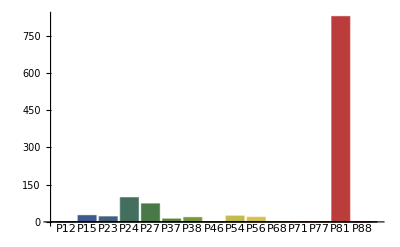

```mathematica
BarChart[{cp12,cp15,cp23,cp24,cp27,cp37,cp38,cp46,cp54,cp56,cp68,cp71,cp77,cp81,cp88},ChartLabels->{"P12","P15","P23","P24","P27","P37","P38","P46","P54","P56","P68","P71","P77","P81","P88"},ChartStyle->"DarkRainbow"]
```

```mathematica
sum=({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}});
```

```mathematica
For[j=1,j<k,j=j+1,sum=sum+storep[j]];
```

```mathematica
sum
```

{{0,355.104,0,0,209.896,0,0,0},{0,0,283.627,113.947,0,0,167.426,0},{0,0,0,0,0,0,315.363,249.637},{0,0,0,0,0,565,0,0},{0,0,0,280.002,0,284.998,0,0},{0,0,0,0,0,0,0,565},{28.25,0,0,0,0,0,536.75,0},{11.3,0,0,0,0,0,0,553.7}}

```mathematica
PFinal=sum/(k-1)
```

{{0,0.636754,0,0,0.363246,0,0,0},{0,0,0.501473,0.214503,0,0,0.284024,0},{0,0,0,0,0,0,0.554387,0.445613},{0,0,0,0,0,1,0,0},{0,0,0,0.48913,0,0.51087,0,0},{0,0,0,0,0,0,0,1},{0.05,0,0,0,0,0,0.95,0},{0.02,0,0,0,0,0,0,0.98}}

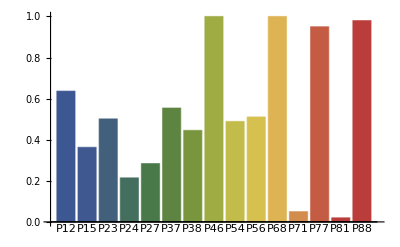

```mathematica
BarChart[{Part[PFinal,1,2],Part[PFinal,1,5],Part[PFinal,2,3],Part[PFinal,2,4],Part[PFinal,2,7],Part[PFinal,3,7],Part[PFinal,3,8],Part[PFinal,4,6],Part[PFinal,5,4],Part[PFinal,5,6],Part[PFinal,6,8],Part[PFinal,7,1],Part[PFinal,7,7],Part[PFinal,8,1],Part[PFinal,8,8]},ChartLabels->{"P12","P15","P23","P24","P27","P37","P38","P46","P54","P56","P68","P71","P77","P81","P88"},ChartStyle->"DarkRainbow"]
```